n = 10

(0
3/5
6/5
9/5
12/5
3
18/5
21/5
24/5
27/5
6) (0.
0.10896
0.28579
0.392638
0.434786
0.443231
0.436737
0.42422
0.409698
0.394953
0.380757)

Найдём аппроксимирующий многочлен 1-го порядка

0.179043+0.0527969 x

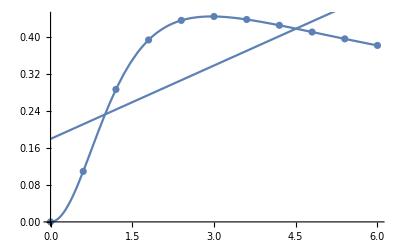

0.109862

Найдём аппроксимирующий многочлен 2-го порядка

{-0.0273509,0.213419,0.045977}

0.045977+0.213419 x-0.0273509 x^2

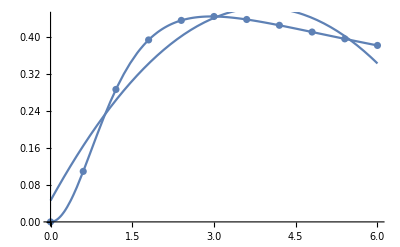

0.0137698

Найдём апроксимирующий многочлен 4-го порядка

-0.0155122+0.29502 x-0.037821 x^2-0.00564349 x^3+0.000936964 x^4

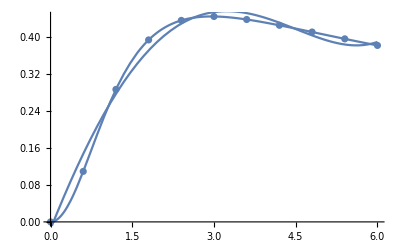

0.00289676

Найдём апроксимирующий многочлен 5-го порядка

-0.00467626+0.153451 x+0.156573 x^2-0.0969181 x^3+0.0183558 x^4-0.00116125 x^5

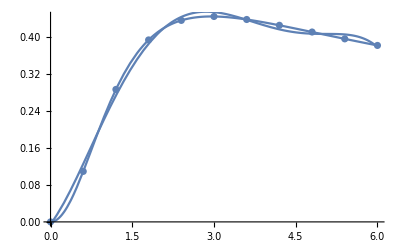

0.00086941

```mathematica
"n = 10"
n = 10; a = 0; b = 6;
h = (b-a)/n;
XDT = {}; YDT = {};
f[x_] :=x^2/(√(2+x^2+√((2+x^2)^5)));

For[i = 0, i<=n,i++,
xdata[i]=a+i*h;
ydata[i]=N[f[xdata[i]]];
XDT = Append[XDT,xdata[i]];
YDT=Append[YDT, ydata[i]];]
MatrixForm[XDT] MatrixForm[YDT]
Array[xdata,{n+1,0}]; Array[ydata,{n+1,0}];
For[i =0,i<=n,i++, xdata[i]=XDT[[i+1]];
ydata[i]=YDT[[i+1]];
];
data=Table[{N[xdata[i]],N[ydata[i]]},{i,0,n}];
"Найдём аппроксимирующий многочлен 1-го порядка"
ex = ∑_(i=0)^n xdata[i]; ey=∑_(i=0)^n ydata[i];exx=∑_(i=0)^n xdata[i]^2;
exy = ∑_(i=0)^n xdata[i]*ydata[i];eyy=∑_(i=0)^n ydata[i]^2;
k=(ey*exx-ex*exy)/((n+1)*exx-ex^2);m=((n+1)*exy-ex*ey)/((n+1)*exx-ex^2);
g[x_]:=k+m*x;
g[x]
gr1:=Plot[N[f[x]],{x,a,b}];
gr2:=ListPlot[Table[{N[xdata[i]],N[ydata[i]]},{i,0,n}]];
gr3:=Plot[g[x],{x,a,b}];
Show[{gr1,gr2,gr3}]
sumq = 0;
For[i=0,i<=n,i++,
xd[i]=a+i*h;
sumq=sumq+Abs[g[xdata[i]]-f[xdata[i]]]^2;];
Print[sumq];
"Найдём аппроксимирующий многочлен 2-го порядка"
A=MatrixForm[({{p*∑_(i=0)^n xdata[i]^4, q*∑_(i=0)^n xdata[i]^3, c*∑_(i=0)^n xdata[i]^2}, {p*∑_(i=0)^n xdata[i]^3, q*∑_(i=0)^n xdata[i]^2, c*∑_(i=0)^n xdata[i]}, {p*∑_(i=0)^n xdata[i]^2, q*∑_(i=0)^n xdata[i], c*n}})];
B=MatrixForm[({{∑_(i=0)^n xdata[i]^2*ydata[i]}, {∑_(i=0)^n xdata[i]*ydata[i]}, {∑_(i=0)^n ydata[i]}})];
A={{∑_(i=0)^n xdata[i]^4,∑_(i=0)^n xdata[i]^3,∑_(i=0)^n xdata[i]^2},{∑_(i=0)^n xdata[i]^3,∑_(i=0)^n xdata[i]^2,∑_(i=0)^n xdata[i]},{∑_(i=0)^n xdata[i]^2,∑_(i=0)^n xdata[i],n}};
B={∑_(i=0)^n xdata[i]^2*ydata[i],∑_(i=0)^n xdata[i]*ydata[i],∑_(i=0)^n ydata[i]};
LinearSolve[A,B]
g[x_]:=-0.0273509x^2+0.213419x+0.045977;
g[x]
gr1:=Plot[N[f[x]],{x,a,b}];
gr2:=ListPlot[Table[{N[xdata[i]],N[ydata[i]]},{i,0,n}]];
gr3:=Plot[g[x],{x,a,b}];
Show[{gr1,gr2,gr3}]
sumq = 0;
For[i=0,i<=n,i++,
xd[i]=a+i*h;
sumq=sumq+Abs[g[xdata[i]]-f[xdata[i]]]^2;];
Print[sumq];
"Найдём апроксимирующий многочлен 4-го порядка"
koefs=FindFit[data,p*x^4+q*x^3+c*x^2+s*x+l,{p,q,c,s,l},x];
y=p*x^4+q*x^3+c*x^2+s*x+l/.koefs
g[x_]:=-0.015512+0.295019 *x-0.037821* x^2-0.005643* x^3+0.000937 *x^4;
gr1:=Plot[N[f[x]],{x,a,b}];
gr2:=ListPlot[Table[{N[xdata[i]],N[ydata[i]]},{i,0,n}]];
gr3:=Plot[y,{x,a,b}];
Show[{gr1,gr2,gr3}]
sumq = 0;
For[i=0,i<=n,i++,
xd[i]=a+i*h;
sumq=sumq+Abs[g[xdata[i]]-f[xdata[i]]]^2;];
Print[sumq];
"Найдём апроксимирующий многочлен 5-го порядка"
Clear[m,p,q,c,s,l];
koefs=FindFit[data,m*x^5+p*x^4+q*x^3+c*x^2+s*x+l,{m,p,q,c,s,l},x];
y=m*x^5+p*x^4+q*x^3+c*x^2+s*x+l/.koefs
g[x_]:=-0.004676+0.153451* x+0.156573* x^2-0.096918* x^3+0.018356 *x^4-0.001161* x^5;
gr1:=Plot[N[f[x]],{x,a,b}];
gr2:=ListPlot[Table[{N[xdata[i]],N[ydata[i]]},{i,0,n}]];
gr3:=Plot[y,{x,a,b}];
Show[{gr1,gr2,gr3}]
sumq = 0;
For[i=0,i<=n,i++,
xd[i]=a+i*h;
sumq=sumq+Abs[g[xdata[i]]-f[xdata[i]]]^2;];
Print[sumq];
```